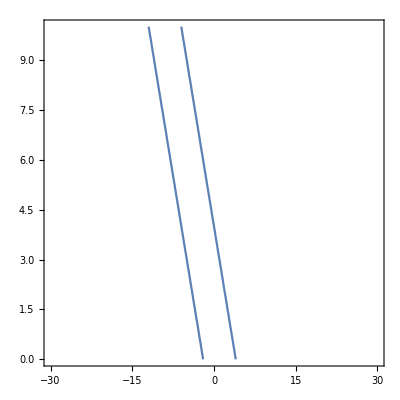

```mathematica
ContourPlot[(1 - x- y)^2== 9, {x,-30,30}, {y, 0, 10}]
```

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = NIntegrate[
1 * Boole[y < (2 - a1 - a2 -x) && y > a1 + a2 - x],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)

pdfSameN[0,1,2]
```

0.5

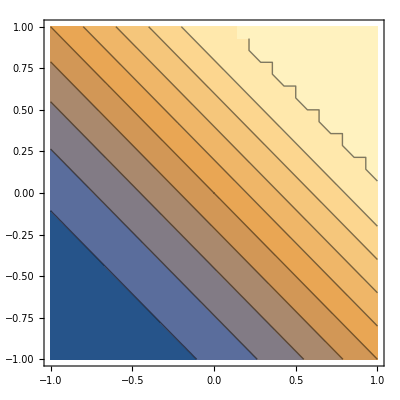

```mathematica
ContourPlot[pdfSameN[x, y, 2], {x,-1,1}, {y, -1, 1}]
```

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = NIntegrate[
1 * Boole[y < (2 - a1 - a2 -x) && y > a1 + a2 - x],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)

pdfSameN[0,1,2]
```

0.5

```mathematica
ContourPlot[pdfSameN[x, y, 2], {x,-1,1}, {y, -1, 1}]
```

-Graphics-

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < (2 - a1 - a2 -x) && y > a1 + a2 - x],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)


fixedPtDist[x0_, y0_, s_] := fixedPtDist[x0, y0, s] = pdfSameN[x0,y0,s]

Plot3D[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

$Aborted

```mathematica
pdfSameN[x0,y0,s]
```

```mathematica
1/4 s (1-1/4 (Piecewise[{{4, x0+y0≤-2}, {-2 (-1+x0+y0), 0≤x0+y0<1}, {1/2 (4-4 x0-x0^2-4 y0-2 x0 y0-y0^2), -2<x0+y0<0}, {0, True}}]))^(-1+s)
```

```mathematica
Integrate[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

25/24

```mathematica
pdfSameN[0,0,2]
```

1/4

```mathematica
pdfSameN[0.5,0,2]
```

0.375

```mathematica
pdfSameN[-0.5,0,2]
```

0.140625

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < (2 - a1 - a2 -x) && y > a1 + a2 - x],
{x, -1, 1},
{y, -1, 1}
];
Print[in];
s/4(1 - 1/4 in)^(s - 1)
)
```

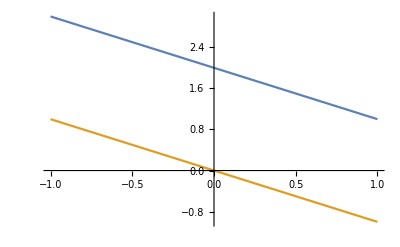

```mathematica
a1 = 0;
a2 = 0;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

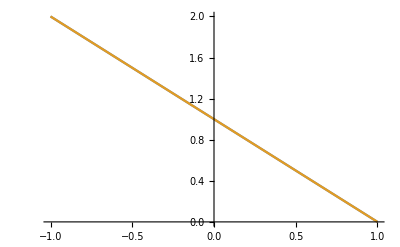

```mathematica
a1 = 0.5;
a2 = 0.5;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

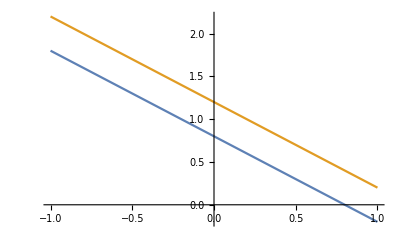

```mathematica
a1 = 0.6;
a2 = 0.6;
Plot[
{ 2 - (a1 + a2)- x, (a1 + a2) -x},
{x, -1, 1}
]
```

```mathematica
pdfSameN[0.1,0.1,2]
```

1.6

0.3

```mathematica
pdfSameN[0.2,0.2,2]
```

1.2

0.35

```mathematica
pdfSameN[0.3,0.3,2]
```

0.8

0.4

```mathematica
pdfSameN[0.5,0.5,2]
```

0.

0.5

```mathematica
pdfSameN[0.7,0.7,2]
```

0.

0.5

```mathematica
pdfSameN[0.63,0.63,2]
```

0.

0.5

```mathematica
ClearAll[pdfSameN];
pdfSameN[a1_, a2_, s_] := pdfSameN[a1, a2, s] = (
in = Integrate[
1 * Boole[y < 1 - x + Abs[1 - a1 - a2] && y >  1 - x - Abs[1 - a1 - a2]],
{x, -1, 1},
{y, -1, 1}
];
s/4(1 - 1/4 in)^(s - 1)
)
```

```mathematica
pdfSameN[0.7,0.7,2]
```

0.4

```mathematica
pdfSameN[0.6,0.6,2]
```

0.45

```mathematica
pdfSameN[0.5,0.5,2]
```

0.5

```mathematica
Integrate[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Integrate[pdfSameN[x0,y0,10], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Integrate[pdfSameN[x0,y0,100], {x0,-1, 1}, {y0 ,-1, 1}]
```

1

```mathematica
Plot3D[pdfSameN[x0,y0,2], {x0,-1, 1}, {y0 ,-1, 1}]
```

-Graphics3D-

```mathematica
pdfSameN[x0,y0,s]
```

1/4 s (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)

```mathematica
Plot3D[Abs[1 - (x0 + y0)], {x0,-1, 1}, {y0 ,-1, 1}]
```

-Graphics3D-

Find the probability of going.

r = t / N

```mathematica
Integrate[
 pdfSameN[x0, y0, 2] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/64 (2+r)^4, -2<r≤0}, {1/24 (6+12 r+3 r^2-2 r^3), 0<r≤1}, {1/24 (-4+36 r-15 r^2+2 r^3), 1<r<2}, {0, True}}]

```mathematica
Solve[1/64 (2+r)^4 == (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-3.38177-1.16904 ⅈ},{r→-3.38177+1.16904 ⅈ},{r→-0.973703-1.80847 ⅈ},{r→-0.973703+1.80847 ⅈ},{r→0.710955}}

```mathematica
Solve[1/24 (6+12 r+3 r^2-2 r^3)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-1.35252-0.841953 ⅈ},{r→-1.35252+0.841953 ⅈ},{r→0.843971},{r→3.36108}}

```mathematica
Solve[1/24 (-4+36 r-15 r^2+2 r^3)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-0.525993},{r→0.848576},{r→3.58871-1.80339 ⅈ},{r→3.58871+1.80339 ⅈ}}

```mathematica
60 / 0.84
```

71.4286

Whoa!  This is right!  The one fixed point at s=2 is in the third case.  What about for more general s?

```mathematica
Integrate[
 pdfSameN[x0, y0, s] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

∫_-1^1 ∫_-1^1 1/4 s Boole[y0<r-x0] (1-1/4 (Piecewise[{{2, Abs[1-x0-y0]==1}, {4, Abs[1-x0-y0]>3}, {2 Abs[1-x0-y0], 0<Abs[1-x0-y0]<1}, {1/2 (-1+6 Abs[1-x0-y0]-Abs[1-x0-y0]^2), 1<Abs[1-x0-y0]≤3}, {0, True}}]))^(-1+s)ⅆy0ⅆx0

```mathematica
Integrate[
 pdfSameN[x0, y0, 3] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {1/512 (2+r)^6, -2<r≤0}, {1/64 (8+24 r+18 r^2-3 r^4), 0<r≤1}, {1/64 (-72+216 r-126 r^2+32 r^3-3 r^4), 1<r<2}, {0, True}}]

```mathematica
Solve[1/64 (8+24 r+18 r^2-3 r^4)== (.6)/r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-2.05308},{r→-0.886784-1.25375 ⅈ},{r→-0.886784+1.25375 ⅈ},{r→0.904798},{r→2.92185}}

```mathematica
60 / 0.9047998
```

66.313

```mathematica
Integrate[
 pdfSameN[x0, y0, 100] * Boole[y0 < r - x0], 
 {x0, -1, 1}, 
 {y0 , -1, 1}]
```

Piecewise[{{1, r≥2}, {(202+20200 r+994850 r^2+32330100 r^3+779838675 r^4+14891244060 r^5+234457885200 r^6+3130329602400 r^7+36175086462900 r^8+367544267675200 r^9+3323769638817320 r^10+27019819397006800 r^11+199072492910300100 r^12+1338398022348567600 r^13+8258895113516770800 r^14+47009015416315333920 r^15+247875860561504509950 r^16+1215391316301570500400 r^17+5559882205712886104900 r^18+23798888226361269452200 r^19+95570466898052138902910 r^20+360895469405231853199800 r^21+1284225436584851010087600 r^22+4314443183651930432493600 r^23+13708016309252308818165300 r^24+41253804196638398690637312 r^25+117761760777663698185413000 r^26+319265218108332692858230800 r^27+823023861435005179540275300 r^28+2019520735622029516182860400 r^29+4721500202592193144730963280 r^30+10526667594132180548201205600 r^31+22399073943196031905121315325 r^32+45521312550658375800382486200 r^33+88416395531086460689204444350 r^34+164226889125067525002918354060 r^35+291865814856625108210968843525 r^36+496545539926776144267878715300 r^37+809016989537447630935308112800 r^38+1262821679433561297726159422400 r^39+1889093128594507685493841973160 r^40+2709013948733822364152203593600 r^41+3724894179509005750709279941200 r^42+4911775290769048356265997047200 r^43+6212128577207291502181626486600 r^44+7536216076762272883397804150880 r^45+8769765511321826501140667234400 r^46+9788838099380500284415605652800 r^47+10479582723328721070614287503300 r^48+10758699938720042939323142618400 r^49+10589634653968727978848064662968 r^50+9990221371668611300800061002800 r^51+9029623162854321752646208983300 r^52+7815282030957012323847943222800 r^53+6473263904429040510661932770400 r^54+5126939837388144723743774690880 r^55+3878934745392346337042987430600 r^56+2799832598177934198166366867200 r^57+1924884911247329761239377221200 r^58+1257756476197846097642094525600 r^59+778841510260973929693758533160 r^60+455203163516748839878034210400 r^61+249627541283378396062147792800 r^62+127261099477800750933643972800 r^63+59369575426027582466811585525 r^64+24578173882663167007239481560 r^65+8378922914544261479740732350 r^66+1750819713486860607707018700 r^67-437704928371715151926754675 r^68-837348558624150725425095900 r^69-669878846899320580340076720 r^70-417831876335592313693005600 r^71-226325599681779169917044700 r^72-110658670445042713215499200 r^73-49721632328346894789396600 r^74-20726069896868810880632688 r^75-8057383632155937244265100 r^76-2929957684420340816096400 r^77-998117452934401816472400 r^78-318712882072152805423200 r^79-95379516914239846917090 r^80-26732997733720878014800 r^81-7009261600914620455100 r^82-1716473701092568864600 r^83-391803779597216806050 r^84-83158353220633771080 r^85-16363897771502173200 r^86-2975254140273122400 r^87-497818776605259900 r^88-76291254768019200 r^89-10648987644702680 r^90-1344877888538800 r^91-152447338297100 r^92-15359254587600 r^93-1358769442800 r^94-103921873440 r^95-6732743325 r^96-359297400 r^97-15165150 r^98-474700 r^99-9797 r^100-100 r^101)/256065421246102339102334047485952, 0<r≤1}, {(-102560126625670254620190343577256294165385349392248+3470208639595542962312171607088516569527523981473400 r-58125994713225344618728874418732652539586026689679450 r^2+642566966431774705188137109245890318124179857236157900 r^3-5273608593314243393157095565733391909555459603901041775 r^4+34270662346306157065284928425199461118648090194415045860 r^5-183672830875627769892376740579500379851577999734773448400 r^6+834954076709880477768597633714476755794513694496984061600 r^7-3286111736371532025975196755019475872623310571909853533700 r^8+11373509649019666400154626235300902000362376042766900475200 r^9-35046449283870215631758518149417587125475603613833647810440 r^10+97105646776099727522532301266546337533396953031805279057200 r^11-243920136544726696514932328181443776423175679639415641441300 r^12+559276356340491348869090189345908515439601254518956656059600 r^13-1177344566851546478347060479458637602583095902370094739575600 r^14+2286885878522909998316700261508702648397713042287576824352480 r^15-4116483634529653998138219220725848127810914539709627675455350 r^16+6892716783398490415487250788192117795404322019978911456576400 r^17-10771642792162867223379767435456612069155519699946467595205300 r^18+15757304930179878691877557763533991331498097942503952192387800 r^19-21633767732123108681096114856081300942740278505465288491659030 r^20+27941852648143349764233729559713617655985486915082368697641800 r^21-34022861902146998886477433788962586787728884893846851141481200 r^22+39129972590980003047481227214297714412957517428571452247314400 r^23-42581753206175311124117146281625027808995436571106846871232900 r^24+43913308179378879896488642096590043626281213152672699242751872 r^25-42978340766219027371219996557445612752370006004504530508874600 r^26+39971625568582305291751930954661351777924367724354007798377200 r^27-35368908886485754545451376747598050314242179152638991940430900 r^28+29808097600216157712010365820397080836004194127121544476000400 r^29-23951067896314035494913592185512040391034948965301170824575760 r^30+18365072017035648196081089373593070366042199211314650869386400 r^31-13449420947258443447945254310280794738174925781112223938314225 r^32+9414418230955142888395103896059073950269107171456752844660200 r^33-6303331746587782451138101171786678823025005663647768427602950 r^34+4039388314858093327976421425353425325460291796226025481625140 r^35-2479064291051322709596165570878111221822140145594557424026825 r^36+1457881779748027232708651710073614189869719372567395471902300 r^37-821927997146077797566340660808674547723160252865828669261600 r^38+444444025720663943766804135315563711946376170488305927617600 r^39-230594242756610585389933602139566634580581305822679174910280 r^40+114838239070543898020499640620582220303422468865667351113600 r^41-54912729396827538537580185296746656930803204358384586544400 r^42+25219336431789494523451056182796126207276147570813314248800 r^43-11127013763762870517578236471335105270640809662629691053800 r^44+4717406109630056490122789600467265480995957347594992933280 r^45-1922155257309467065944543636208448633857939380167596312800 r^46+752837187187641899036898983873217832279575041646188395200 r^47-283461562858761507716637269842507324044291212327147154900 r^48+102614194337920660371463831964799809062165405128976898400 r^49-35716359900198836303486927319360965799379507140053572056 r^50+11953266365528392337177686519197110374625002389576162000 r^51-3846499817625162149527691431177531671834455897158482900 r^52+1190122021299343562163119441533993863133926217597858800 r^53-354028067476465515846289498774956434300862237568792800 r^54+101242952917332502770942724550854711047639079940022720 r^55-27830423643614319870246488540062002263517210529069800 r^56+7352516463122049418764810181894605345160377601075200 r^57-1866519759450972854422424423869975692418138243376400 r^58+455212693428061571961625372252929506731008060674400 r^59-106627986199622174414267028410150025284666358398280 r^60+23981567037744422205120292905715536205551899498400 r^61-5177162114848051443785274150861666625019888973600 r^62+1072396409607277456518436037087808582668475451200 r^63-213055218623074326106179424194011589042397098825 r^64+40579572497030126107149470908201329857972796360 r^65-7406051454347784723412265696056027832205778950 r^66+1294477406176248489157386532061984776454253300 r^67-216557310431740818674825942393828280271482225 r^68+34652931181282740783443895032134059069659100 r^69-5300149815360373714710111024104654947967760 r^70+774250902395698343580355503285616383309600 r^71-107933124768124614768660669439507222158900 r^72+14345254143641290692264323923551078676800 r^73-1815963213334559254962713501451120253800 r^74+218713811188426037740564175559387670128 r^75-25032074369273373188709083353336244100 r^76+2718950226650708776105354980527667600 r^77-279877076470548617978886410110057200 r^78+27259120884593639862861577575343200 r^79-2507741066990943667239873548523030 r^80+217495132143114721350066469981200 r^81-17745682965219290563115179461300 r^82+1358907077815103243395948656600 r^83-97408992659998535430864607350 r^84+6516879603165979755563144520 r^85-405570627121367885213559600 r^86+23390441491573142805218400 r^87-1244739270941153949345300 r^88+60816451087756337500800 r^89-2712338636475552706440 r^90+109666530417595258800 r^91-3987126480699677700 r^92+129058966008680400 r^93-3673785780680400 r^94+90541298564640 r^95-1892692961775 r^96+32630736600 r^97-445455450 r^98+4514700 r^99-30199 r^100+100 r^101)/256065421246102339102334047485952, 1<r<2}, {(1606938044258990275541962092341162602522202993782792835301376+160693804425899027554196209234116260252220299378279283530137600 r+7994516770188476620821261409397283947547959894069394355624345600 r^2+263819053416219728487101626510110370269082676504290013735603404800 r^3+6496544190374410813994877552811467867876160908918141588239233843200 r^4+127332266131338451954299600035104770210372753814795575129488983326720 r^5+2069149324634249844257368500570452515918557249490428095854195979059200 r^6+28672497784217462127566392079333413434871436171510217899693858566963200 r^7+345862004522123136913769604456959299558136698818842003415057168963993600 r^8+3689194714902646793746875780874232528620124787400981369760609802282598400 r^9+35231809527320276880282663707348920648322191719679372081213823611798814720 r^10+304274718645038754875168459290740678326418928488140031610483022101898854400 r^11+2396163409329680194641951616914582841820549061844102748932553799052453478400 r^12+17326104652076149099718727076151599010087047062565050646127696700840817459200 r^13+115713627497794281487407212972869607674509921453559445386638545823472602316800 r^14+717424490486324545221924720431791567581961513012068561397158984105530134364160 r^15+4147610335624063777064252289996295000083214997101021370577325376860096089292800 r^16+22445891228083168675877130039979949412215045866664350946653760863007578836172800 r^17+114099947076089440769042077703231409512093149822210450645489951053621859083878400 r^18+546478693890744163683306793210213592926340875464271105723136081362083640875417600 r^19+2472816089855617340666963239276216507991692461475826753397190768163428474961264640 r^20+10597783242238360031429842454040927891392967692039257514559389006414693464119705600 r^21+43113709099106055582407768165302865739985027656250615797866605276096139319941529600 r^22+166831309122627780297143102900519784819942063539404556783049037807502452151078092800 r^23+615190452389689939845715191945666706523536359301554303137493326915165292307100467200 r^24+2165470392411708588256917475648746806962847984741471147043976510741381828920993644544 r^25+7287640743693250056633856889202513292663430717879950975628767103456573462714882457600 r^26+23482397951900472404709094420763653943026610090946508699248249555582292268747954585600 r^27+72543836529978245107404880978430573788278634745245464374463342377066724330239216844800 r^28+215129997985452726870235164280863080889378020279003790903580946359577182496571470643200 r^29+613120494258540271580170218200459780534727357795160804075205697124794970115228691333120 r^30+1681136839095997518848853824098034882111349206857698978915886588890566853541756089139200 r^31+4439251965737868448210254629258873360575281499358611366199763023789153097633699672883200 r^32+11299914094605483322717011783568041281464352907458283477599396787826935157613053712793600 r^33+27751259614692878160202073056703866088302160816846078540574989170104384872373234853478400 r^34+65810129943414539637050630391612025295116552794234986253363545746247541268770814081105920 r^35+150814881120324986668241027980777557967975433486788510163958125668483948740933115602534400 r^36+334238385185585105589074710660101614956053663403152914417420710940964426939365283227238400 r^37+716853378753294371197620761021007411024167725456762171711047051097068441988375541658419200 r^38+1488849325102996001718135426735938469050194506717890664322943875355449841052779971136716800 r^39+2996309266769779453457747546306076168963516444769754961949924549152842805118719691912642560 r^40+5846457105892252592112678139133807158953202819062936511121803998347010351451160374463692800 r^41+11066508093296049549356140763360420693732848193226272681766271854013983879532553565949132800 r^42+20331491613264835218584537681522633367555697843369198647896173871328016894955156551394918400 r^43+36273229355483853742247413818171061803480051834192774860451128384073848323954086120102297600 r^44+62873597549505346486562183951496507126032089845934143091448622532394670428187082608177315840 r^45+105928343697536181580621070787847376136249716588258610643201483614360586047489106568124825600 r^46+173542180100218850674634520226898892818962301644593894032479026346931172886311940547778969600 r^47+276582849534723793262698766611620110430221168246071518614263448240421556787559655248022732800 r^48+428985644176306291591124617601696497810138954830641539075184123801470169711317016303055667200 r^49+647768322706222500302598172578561711693309821794268724003528026940219956264088694617614057472 r^50+952600474567974265150879665556708399548985032050395182358129451382676406270718668555314790400 r^51+1364783372217578514495010290076437995507680478610662328570781617846334466676318092449441382400 r^52+1905546595171713397596806820106724748444685951267717213476185655106202840265047902665257779200 r^53+2593660643428165457840098171811930907605266989225503985009252697227887199249648534183267532800 r^54+3442495035822837789496857573495835568276081640244759834648644489047923009913169872643245998080 r^55+4456801608877781066759324537115144262500284266388305143071905811713828896762585995832773836800 r^56+5629644137529828715906515204777024331579306441753648601775038920059573343279055994736135372800 r^57+6939992341954875054953721330026848960481386389403204741843366944556198173180215579717822054400 r^58+8351516208115188625452783295456038579562346333010636214760661916330340174505005189151955353600 r^59+9813031544535346634907020372160845330985756941287497552343777751688149705043381097253547540480 r^60+11260855870778266630221170918873101199491852227706964404328925288822466874639945521438497177600 r^61+12623056177727250496780183530027105376849737577832806872594521089889700770765745382902831513600 r^62+13825252004177464829806867675743972555597331632864502765222570717498243701314863990798339276800 r^63+14797340035721192825652663059194720625912769013300288115902282721072338961563565365151347507200 r^64+15480294191216017109913555200388323116339512198529532182790080385121831529020345305081409699840 r^65+15832119059198199316957045091306239550801773839405203368762582212056418609225353152924169011200 r^66+15832119059198199316957045091306239550801773839405203368762582212056418609225353152924169011200 r^67+15482881138774709626141816155468601913651734710594794470922231133849291728139499774550841753600 r^68+14809712393610591816309563279143880091319050592742846885229960214986279044307347610439935590400 r^69+13857659454021339485261091354056059228305683054637949585465177058308589677173303835483082588160 r^70+12686589641005451641436210394558364082251681669738967930355443785775469422764292243752117862400 r^71+11365069886734050428786605145125201157017131495807825437610085058090524691226345135027938918400 r^72+9963896886999715444415653825863190055467074188105490794617060872846487400527206693723124531200 r^73+8550100707087593658383702945166386061110259607360792776461937370618269593695643581775924428800 r^74+7182084593953578673042310473939764291332618070183065932228027391319346458704340608691776520192 r^75+5906319567396035092962426376595200897477481965611073957424364631019199390381859053200474112000 r^76+4755737833487716568359356303232499423942907556725799809874163728872602106541237159719862272000 r^77+3749716368711468832744877085241009161185754035110726773170013709303397814772898529779122176000 r^78+2895350613815184794904272179743057706738367039769042191941402990727940084824643168563625984000 r^79+2189608901697733501146355835930687390720890073825338157655686011738004689148636396226242150400 r^80+1621932519776098889738041359948657326459918573203954190856063712398521991961952886093512704000 r^81+1176890060081437609017237328255428182004453111044332614096777937655025103923612155153219584000 r^82+836584500539817095566469908036991117328466669296573785924215642429475676283049604265541632000 r^83+582621348590229762983791543097190242425182144688685315197221608120527703125695260113502208000 r^84+397553390802745014741881288231023930125418404611102920958104156129301256250474412783330918400 r^85+265806046176253934275095047363765999793157654245795557617337081132963049237235799244668928000 r^86+174148788874097405214717444824536344692068807954141917059634639362975790879568282263748608000 r^87+111811438311210265848085632188480721307975996016011571748515421863728774826086453953429504000 r^88+70353264555368257162840397781515959474681525583108404695695096903020352699560015970697216000 r^89+43384513142477091917084911965268175009386940776250182895678643090195884164728676515263283200 r^90+26221409042156484125710661077909336544134964205425934717168410658909600319341507783950336000 r^91+15533334704320960704904685095065856974514734230388189587887808488158404537001219285057536000 r^92+9019355634767009441557559087457594372298877940225400405870340412479073602129740230033408000 r^93+5133356664468457501312015012542354243808403934064456613979395873059898273552564918157312000 r^94+2863872665440297342837229428049944999177320089530696847799031381812364299981957270129868800 r^95+1566180363912662609364109843464813671425096923962099838640095286928636726552632882102272000 r^96+839601844571736656566326926393508359939227216969373109374071700209166080213782575972352000 r^97+441219336688208549113937109278221229968063282386966480946578495518082174806222476148736000 r^98+227294809809077131361725177506962451801729569714497884123994982539618090051690366500864000 r^99+114783878953583951337671214641016038159873432705821431482617466182507135476103635082936320 r^100+56823702452269282840431294376740612950432392428624471030998745634904522512922591625216000 r^101+27576208543013034319621069329888826873003955149185405059161155969880135925388904759296000 r^102+13118778821433385258848858224898568124050425265146454833969870315768220003340352749568000 r^103+6117892046533838317828554076034428404004284859226952494687872214564987213096222195712000 r^104+2796750649844040373864481863330024413259101649932321140428741583801137011701130146611200 r^105+1253260904411244507156253665171473204054786116714955228022313445571264226941544169472000 r^106+550497780442322353610690862271581687762382686781335473991109644316349707161239027712000 r^107+237019877690444346693491899033597671119914767919741662412838874636206123916644581376000 r^108+100026737373948990347712177573811861206569535085395563954042093883169556882253676544000 r^109+41374695913769809643826400723713088044535580421686346908262866106220134892204929843200 r^110+16773525370447220125875567860964765423460370441224194692538999772791946577920917504000 r^111+6664481062365190139298774730472607690571307898522113069803441874011085917120364544000 r^112+2595019174726268726806602549918537507833075641902415708596030464216706020825628672000 r^113+990204685092918329965677288784705101673147284410132309859011624503743086893989888000 r^114+370250447469525984248035855806454951060394201996832081077717390031834371621231001600 r^115+135652103598748744228806240273916684655747875731597960739680940313387593050882048000 r^116+48695626932884164594956086252175220132832570775445421803988029856087853915701248000 r^117+17126004387412651107548115080214166402648743111703262753097485076505474046623744000 r^118+5900556133478308364785485027636813634526037542687678763672242757451465847996416000 r^119+1991437695048929073115101196827424601652537670657091582739381930639869723698790400 r^120+658326510759976553095901222091710612116541378729617052145250225004915611140096000 r^121+213146698155894047928590969447725976873798233277212078358503146620443988852736000 r^122+67583099415283478611504453727327748764862854453750171186842461123555411099648000 r^123+20983462318454951020507431197597728447154999165075657989463183494007123607552000 r^124+6378972544810305110234259084069709447935119746183000028796807782178165576695808 r^125+1898503733574495568522100917877889716647357067316369056189526125648263564492800 r^126+553107386946900283742659322531353696976001665281146890385924934243982298316800 r^127+157722028309077034035992697440581327653312974865327042961611407030510577254400 r^128+44015449760672660661207264402022696089296644148463360826496206613165742489600 r^129+12019603588491380411329676048244659316692545132849610071850887190518337372160 r^130+3211344470207620720584264593042466229650679997326231698586114898230090137600 r^131+839328668349719051970887336817917310022336817482992375766825484764682649600 r^132+214565223487898103511354657532399913840296630033246171248662153999994060800 r^133+53641305871974525877838664383099978460074157508311542812165538499998515200 r^134+13112319213149328547916117960313328068018127390920599354084909411110748160 r^135+3133458635495243954465248777280758545666096619153819698586467322508083200 r^136+731902746976991288634218692503534842783321838050527228866912075330355200 r^137+167064757462139315883897745027980779330975636946315997893534278064537600 r^138+37259046628246897787056331624945353663742767952056085861147932517990400 r^139+8117149444010931303608700818291666333886817303840790134035799584276480 r^140+1727053073193815170980574642189716241252514319966125560433148847718400 r^141+358789194783222165802302478483074852936261777739441577695618950758400 r^142+72761445095898201456410992139924270875185954926180459812398248755200 r^143+14400702675229852371581342194360011944047220245806549337870486732800 r^144+2780825344182316320029500561669519547816014944017816423864645713920 r^145+523785595650778758909666201684327312088632951784177751070395596800 r^146+96205517568510384289530526839978485893830542164440811421093068800 r^147+17225987943010305295084857846347499163422360590254604747695718400 r^148+3005877090726630454175881234933120659389136747292749821745561600 r^149+510999105423527177209899809938630512096153247039767469696745472 r^150+84602500897934963114221822837521607962939279311219779751116800 r^151+13636587315785569712489701707363680230868502257400556604620800 r^152+2139072520123226621567012032527636114646039569788322604646400 r^153+326416910538284581862498589379217199312869674610555722137600 r^154+48436057692777712147338500359496745704490338813179236188160 r^155+6985969859535246944327668321081261399686106559593159065600 r^156+978925712801117406211520401680176756643913021089487257600 r^157+133208245729265976161694231874201267518000822490025164800 r^158+17593541888770977983619992889045450426905769008116531200 r^159+2254172554498781554151311588908948335947301654164930560 r^160+280021435341463547099541812286825880241900826604339200 r^161+33706283883694686224944847775266078177265840239411200 r^162+3928953336136190418858601887914450830478840273305600 r^163+443205101942192211883439847112300855877186250342400 r^164+48349647484602786750920710594069184277511227310080 r^165+5097101391449088964705496598772353764195460710400 r^166+518866608710386301796367917240299484977981030400 r^167+50960113355484368926428991871815127988908851200 r^168+4824626116495561555164874970112674839186636800 r^169+439892381209889435912091541392626235337605120 r^170+38587050983323634729130836964265459240140800 r^171+3252978135222050602165099627801448598732800 r^172+263246785509298892660759507452140349030400 r^173+20424319565376638223679616957493647769600 r^174+1517235167713693125187628688270956691456 r^175+107758179525120250368439537519244083200 r^176+7305639289838661041928104238592819200 r^177+471993549624407876304343813167513600 r^178+29005190200382606923730625390182400 r^179+1691969428355652070550953147760640 r^180+93478973942301219367455975014400 r^181+4879396991493744966982592102400 r^182+239970343843954670507340595200 r^183+11085586536269645104958668800 r^184+479376715081930599133347840 r^185+19329706253303653190860800 r^186+723571891834896108748800 r^187+25017113281525663334400 r^188+794194072429386137600 r^189+22989828412429598720 r^190+601827968911769600 r^191+14105343021369600 r^192+292338715468800 r^193+5274152083200 r^194+81140801280 r^195+1034959200 r^196+10507200 r^197+79600 r^198+400 r^199+r^200)/2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397376, -2<r≤0}, {0, True}}]